# Mathematica Basics

## Basics

Mathematica is a rich-text mathematics editor - much like Jupyter Notebooks or .mlx files in MATLAB. .nb files can be formatted just like Word documents, where you can mix in equations, executable code, and pictures. 
The number one thing to remember in Mathematica is all built-in functions are Capitalized and take arguments between square brackets [ ]

## A notebook is made from “cells”

Everything in Mathematica from text to input is contained within cells.

Any formatting will apply to the entire cell

Press Shift+Enter to evaluate cell

Press Ctrl+Shift+d to divide cell

Press Alt+Enter to start new cell of the same type

```mathematica
X=0
```

0

## Lists

Mathematica is build on lists. They are the most general structure in Mathematica. You can build them in several ways:

```mathematica
flist = {3,4,5,6,7,8}
slist = List[3,4,5,6,7,8]
rlist = Range[3,8]
rlist2 = Range[3,8,1/4]//N
mixlist = {2,"catch",4,5,True}
```

{3,4,5,6,7,8}

{3,4,5,6,7,8}

{3,4,5,6,7,8}

{3.,3.25,3.5,3.75,4.,4.25,4.5,4.75,5.,5.25,5.5,5.75,6.,6.25,6.5,6.75,7.,7.25,7.5,7.75,8.}

{2,catch,4,5,True}

You can use indexing to extract elements just as in MATLAB or Python:

```mathematica
flist[[4]]
flist[[2;;5]]
3*flist[[3;;]]
3*mixlist[[2]]
```

6

{4,5,6,7}

{15,18,21,24}

3 catch

You can apply functions directly to list - the functions will return lists :

```mathematica
Sqrt[flist]
Sqrt[flist]//N
Log[flist]//N
```

{√3,2,√5,√6,√7,2 √2}

{1.73205,2.,2.23607,2.44949,2.64575,2.82843}

{1.09861,1.38629,1.60944,1.79176,1.94591,2.07944}

There is a plethora of useful functions you can use to manipulate lists:

```mathematica
v=RandomInteger[{1,50},10]
```

{45,29,7,26,8,27,34,7,50,7}

```mathematica
Sort[v]
Union[v]
Reverse[v]
Prepend[v,4.5]
Append[v,4.5]
Delete[v,6]
```

{7,7,7,8,26,27,29,34,45,50}

{7,8,26,27,29,34,45,50}

{7,50,7,34,27,8,26,7,29,45}

{4.5,45,29,7,26,8,27,34,7,50,7}

{45,29,7,26,8,27,34,7,50,7,4.5}

{45,29,7,26,8,34,7,50,7}

## Import Data

Mathematica can import numerous file formats, including ones produced by other programs. (When importing files, be extra careful with your directory path).

```mathematica
SetDirectory["C:\Users\Tom K\Google Drive\Programs\courses\CompProbSol\Mathematica"]
sun = Import["yearlysunspots.csv"];
```

C:\Users\Tom K\Google Drive\Programs\courses\CompProbSol\Mathematica

It will most likely be imported as a nested list - a list of lists. Use the same syntax to extract elements

```mathematica
sun=Flatten[sun]
sun = Partition[sun,5]
sun[[9]];
sun[[9,2]];
sun[[All,2]];
ListPlot[sun[[All,2]],Joined->True];
```

{1818.5,52.9,9.2,213,1,1819.5,38.5,7.9,249,1,1820.5,24.2,6.4,224,1,1821.5,9.2,4.2,304,1,1822.5,6.3,3.7,353,1,1823.5,2.2,2.7,302,1,1824.5,11.4,4.6,194,1,1825.5,28.2,6.8,310,1,1826.5,59.9,9.8,320,1,1827.5,83,11.6,321,1,1828.5,108.5,13.2,301,1,1829.5,115.2,13.6,291,1,1830.5,117.4,13.7,268,1,1831.5,80.8,11.4,285,1,1832.5,44.3,8.5,277,1,1833.5,13.4,4.9,292,1,1834.5,19.5,5.8,260,1,1835.5,85.8,11.8,173,1,1836.5,192.7,17.6,166,1,1837.5,227.3,19.1,150,1,1838.5,168.7,16.5,201,1,1839.5,143,15.1,194,1,1840.5,105.5,13,248,1,1841.5,63.3,10.1,277,1,1842.5,40.3,8.1,311,1,1843.5,18.1,5.6,320,1,1844.5,25.1,6.5,294,1,1845.5,65.8,10.3,265,1,1846.5,102.7,12.8,247,1,1847.5,166.3,16.3,232,1,1848.5,208.3,18.3,234,1,1849.5,182.5,16.6,365,1,1850.5,126.3,13.7,365,1,1851.5,122,13.4,365,1,1852.5,102.7,12.3,366,1,1853.5,74.1,10.4,365,1,1854.5,39,7.5,365,1,1855.5,12.7,4.3,365,1,1856.5,8.2,3.4,366,1,1857.5,43.4,8,365,1,1858.5,104.4,12.4,365,1,1859.5,178.3,16.3,365,1,1860.5,182.2,16.5,366,1,1861.5,146.6,14.8,365,1,1862.5,112.1,12.9,365,1,1863.5,83.5,11.1,365,1,1864.5,89.2,11.5,366,1,1865.5,57.8,9.2,365,1,1866.5,30.7,6.7,365,1,1867.5,13.9,4.5,365,1,1868.5,62.8,8.9,366,1,1869.5,123.6,12.5,365,1,1870.5,232,17.1,365,1,1871.5,185.3,15.3,365,1,1872.5,169.2,14.6,366,1,1873.5,110.1,11.8,365,1,1874.5,74.5,9.7,365,1,1875.5,28.3,6.1,365,1,1876.5,18.9,5.1,366,1,1877.5,20.7,5.3,365,1,1878.5,5.7,3.2,365,1,1879.5,10,3.9,365,1,1880.5,53.7,8.3,366,1,1881.5,90.5,10.7,365,1,1882.5,99,11.2,365,1,1883.5,106.1,11.6,365,1,1884.5,105.8,11.6,366,1,1885.5,86.3,10.5,365,1,1886.5,42.4,7.4,365,1,1887.5,21.8,5.4,365,1,1888.5,11.2,4,366,1,1889.5,10.4,3.9,365,1,1890.5,11.8,4.1,365,1,1891.5,59.5,8.7,365,1,1892.5,121.7,12.4,366,1,1893.5,142,10.6,365,1,1894.5,130,10.2,365,1,1895.5,106.6,9.2,365,1,1896.5,69.4,7.4,366,1,1897.5,43.8,5.9,365,1,1898.5,44.4,6,365,1,1899.5,20.2,4.1,365,1,1900.5,15.7,3.8,365,1,1901.5,4.6,2.6,365,1,1902.5,8.5,3.1,365,1,1903.5,40.8,5.7,365,1,1904.5,70.1,7.5,366,1,1905.5,105.5,9.2,365,1,1906.5,90.1,8.5,365,1,1907.5,102.8,9,365,1,1908.5,80.9,8,366,1,1909.5,73.2,7.6,365,1,1910.5,30.9,5,365,1,1911.5,9.5,3.1,365,1,1912.5,6,2.7,366,1,1913.5,2.4,2.3,365,1,1914.5,16.1,3.8,365,1,1915.5,79,7.9,365,1,1916.5,95,8.7,366,1,1917.5,173.6,11.8,365,1,1918.5,134.6,10.3,365,1,1919.5,105.7,9.2,365,1,1920.5,62.7,7.1,366,1,1921.5,43.5,5.9,365,1,1922.5,23.7,4.5,365,1,1923.5,9.7,3.1,365,1,1924.5,27.9,4.8,366,1,1925.5,74,7.7,365,1,1926.5,106.5,9.2,365,1,1927.5,114.7,9.5,365,1,1928.5,129.7,10.2,366,1,1929.5,108.2,9.3,365,1,1930.5,59.4,6.9,365,1,1931.5,35.1,5.3,365,1,1932.5,18.6,4,366,1,1933.5,9.2,3.2,365,1,1934.5,14.6,3.6,365,1,1935.5,60.2,6.9,365,1,1936.5,132.8,10.3,366,1,1937.5,190.6,12.3,365,1,1938.5,182.6,12.1,365,1,1939.5,148,10.8,365,1,1940.5,113,9.5,366,1,1941.5,79.2,7.9,365,1,1942.5,50.8,6.4,365,1,1943.5,27.1,4.7,365,1,1944.5,16.1,3.8,366,1,1945.5,55.3,6.6,365,1,1946.5,154.3,11.1,365,1,1947.5,214.7,9.8,365,1,1948.5,193,9.3,366,1,1949.5,190.7,9.2,365,1,1950.5,118.9,7.3,365,1,1951.5,98.3,6.6,365,1,1952.5,45,4.5,366,1,1953.5,20.1,3,365,1,1954.5,6.6,1.7,365,1,1955.5,54.2,4.9,365,1,1956.5,200.7,9.5,366,1,1957.5,269.3,11,365,1,1958.5,261.7,10.8,365,1,1959.5,225.1,10,365,1,1960.5,159,8.4,366,1,1961.5,76.4,5.8,365,1,1962.5,53.4,4.9,365,1,1963.5,39.9,4.2,365,1,1964.5,15,2.6,366,1,1965.5,22,3.2,365,1,1966.5,66.8,5.4,365,1,1967.5,132.9,7.7,365,1,1968.5,150,8.2,366,1,1969.5,149.4,8.2,365,1,1970.5,148,8.1,365,1,1971.5,94.4,6.5,365,1,1972.5,97.6,6.6,366,1,1973.5,54.1,4.9,365,1,1974.5,49.2,4.7,365,1,1975.5,22.5,3.2,365,1,1976.5,18.4,2.9,366,1,1977.5,39.3,4.2,365,1,1978.5,131,7.6,365,1,1979.5,220.1,9.9,365,1,1980.5,218.9,9.9,366,1,1981.5,198.9,13.1,3049,1,1982.5,162.4,12.1,3436,1,1983.5,91,7.6,4216,1,1984.5,60.5,5.9,5103,1,1985.5,20.6,3.7,5543,1,1986.5,14.8,3.5,5934,1,1987.5,33.9,3.7,6396,1,1988.5,123,8.4,6556,1,1989.5,211.1,12.8,6932,1,1990.5,191.8,11.2,7108,1,1991.5,203.3,12.7,6932,1,1992.5,133,8.9,7845,1,1993.5,76.1,5.8,8010,1,1994.5,44.9,4.4,8524,1,1995.5,25.1,3.7,8429,1,1996.5,11.6,3.1,7614,1,1997.5,28.9,3.6,7294,1,1998.5,88.3,6.6,6353,1,1999.5,136.3,9.3,6413,1,2000.5,173.9,10.1,5953,1,2001.5,170.4,10.5,6558,1,2002.5,163.6,9.8,6588,1,2003.5,99.3,7.1,7087,1,2004.5,65.3,5.9,6882,1,2005.5,45.8,4.7,7084,1,2006.5,24.7,3.5,6370,1,2007.5,12.6,2.7,6841,1,2008.5,4.2,2.5,6644,1,2009.5,4.8,2.5,6465,1,2010.5,24.9,3.4,6328,1,2011.5,80.8,6.7,6077,1,2012.5,84.5,6.7,5753,1,2013.5,94,6.9,5347,1,2014.5,113.3,8,5273,1,2015.5,69.8,6.4}

{{1818.5,52.9,9.2,213,1},{1819.5,38.5,7.9,249,1},{1820.5,24.2,6.4,224,1},{1821.5,9.2,4.2,304,1},{1822.5,6.3,3.7,353,1},{1823.5,2.2,2.7,302,1},{1824.5,11.4,4.6,194,1},{1825.5,28.2,6.8,310,1},{1826.5,59.9,9.8,320,1},{1827.5,83,11.6,321,1},{1828.5,108.5,13.2,301,1},{1829.5,115.2,13.6,291,1},{1830.5,117.4,13.7,268,1},{1831.5,80.8,11.4,285,1},{1832.5,44.3,8.5,277,1},{1833.5,13.4,4.9,292,1},{1834.5,19.5,5.8,260,1},{1835.5,85.8,11.8,173,1},{1836.5,192.7,17.6,166,1},{1837.5,227.3,19.1,150,1},{1838.5,168.7,16.5,201,1},{1839.5,143,15.1,194,1},{1840.5,105.5,13,248,1},{1841.5,63.3,10.1,277,1},{1842.5,40.3,8.1,311,1},{1843.5,18.1,5.6,320,1},{1844.5,25.1,6.5,294,1},{1845.5,65.8,10.3,265,1},{1846.5,102.7,12.8,247,1},{1847.5,166.3,16.3,232,1},{1848.5,208.3,18.3,234,1},{1849.5,182.5,16.6,365,1},{1850.5,126.3,13.7,365,1},{1851.5,122,13.4,365,1},{1852.5,102.7,12.3,366,1},{1853.5,74.1,10.4,365,1},{1854.5,39,7.5,365,1},{1855.5,12.7,4.3,365,1},{1856.5,8.2,3.4,366,1},{1857.5,43.4,8,365,1},{1858.5,104.4,12.4,365,1},{1859.5,178.3,16.3,365,1},{1860.5,182.2,16.5,366,1},{1861.5,146.6,14.8,365,1},{1862.5,112.1,12.9,365,1},{1863.5,83.5,11.1,365,1},{1864.5,89.2,11.5,366,1},{1865.5,57.8,9.2,365,1},{1866.5,30.7,6.7,365,1},{1867.5,13.9,4.5,365,1},{1868.5,62.8,8.9,366,1},{1869.5,123.6,12.5,365,1},{1870.5,232,17.1,365,1},{1871.5,185.3,15.3,365,1},{1872.5,169.2,14.6,366,1},{1873.5,110.1,11.8,365,1},{1874.5,74.5,9.7,365,1},{1875.5,28.3,6.1,365,1},{1876.5,18.9,5.1,366,1},{1877.5,20.7,5.3,365,1},{1878.5,5.7,3.2,365,1},{1879.5,10,3.9,365,1},{1880.5,53.7,8.3,366,1},{1881.5,90.5,10.7,365,1},{1882.5,99,11.2,365,1},{1883.5,106.1,11.6,365,1},{1884.5,105.8,11.6,366,1},{1885.5,86.3,10.5,365,1},{1886.5,42.4,7.4,365,1},{1887.5,21.8,5.4,365,1},{1888.5,11.2,4,366,1},{1889.5,10.4,3.9,365,1},{1890.5,11.8,4.1,365,1},{1891.5,59.5,8.7,365,1},{1892.5,121.7,12.4,366,1},{1893.5,142,10.6,365,1},{1894.5,130,10.2,365,1},{1895.5,106.6,9.2,365,1},{1896.5,69.4,7.4,366,1},{1897.5,43.8,5.9,365,1},{1898.5,44.4,6,365,1},{1899.5,20.2,4.1,365,1},{1900.5,15.7,3.8,365,1},{1901.5,4.6,2.6,365,1},{1902.5,8.5,3.1,365,1},{1903.5,40.8,5.7,365,1},{1904.5,70.1,7.5,366,1},{1905.5,105.5,9.2,365,1},{1906.5,90.1,8.5,365,1},{1907.5,102.8,9,365,1},{1908.5,80.9,8,366,1},{1909.5,73.2,7.6,365,1},{1910.5,30.9,5,365,1},{1911.5,9.5,3.1,365,1},{1912.5,6,2.7,366,1},{1913.5,2.4,2.3,365,1},{1914.5,16.1,3.8,365,1},{1915.5,79,7.9,365,1},{1916.5,95,8.7,366,1},{1917.5,173.6,11.8,365,1},{1918.5,134.6,10.3,365,1},{1919.5,105.7,9.2,365,1},{1920.5,62.7,7.1,366,1},{1921.5,43.5,5.9,365,1},{1922.5,23.7,4.5,365,1},{1923.5,9.7,3.1,365,1},{1924.5,27.9,4.8,366,1},{1925.5,74,7.7,365,1},{1926.5,106.5,9.2,365,1},{1927.5,114.7,9.5,365,1},{1928.5,129.7,10.2,366,1},{1929.5,108.2,9.3,365,1},{1930.5,59.4,6.9,365,1},{1931.5,35.1,5.3,365,1},{1932.5,18.6,4,366,1},{1933.5,9.2,3.2,365,1},{1934.5,14.6,3.6,365,1},{1935.5,60.2,6.9,365,1},{1936.5,132.8,10.3,366,1},{1937.5,190.6,12.3,365,1},{1938.5,182.6,12.1,365,1},{1939.5,148,10.8,365,1},{1940.5,113,9.5,366,1},{1941.5,79.2,7.9,365,1},{1942.5,50.8,6.4,365,1},{1943.5,27.1,4.7,365,1},{1944.5,16.1,3.8,366,1},{1945.5,55.3,6.6,365,1},{1946.5,154.3,11.1,365,1},{1947.5,214.7,9.8,365,1},{1948.5,193,9.3,366,1},{1949.5,190.7,9.2,365,1},{1950.5,118.9,7.3,365,1},{1951.5,98.3,6.6,365,1},{1952.5,45,4.5,366,1},{1953.5,20.1,3,365,1},{1954.5,6.6,1.7,365,1},{1955.5,54.2,4.9,365,1},{1956.5,200.7,9.5,366,1},{1957.5,269.3,11,365,1},{1958.5,261.7,10.8,365,1},{1959.5,225.1,10,365,1},{1960.5,159,8.4,366,1},{1961.5,76.4,5.8,365,1},{1962.5,53.4,4.9,365,1},{1963.5,39.9,4.2,365,1},{1964.5,15,2.6,366,1},{1965.5,22,3.2,365,1},{1966.5,66.8,5.4,365,1},{1967.5,132.9,7.7,365,1},{1968.5,150,8.2,366,1},{1969.5,149.4,8.2,365,1},{1970.5,148,8.1,365,1},{1971.5,94.4,6.5,365,1},{1972.5,97.6,6.6,366,1},{1973.5,54.1,4.9,365,1},{1974.5,49.2,4.7,365,1},{1975.5,22.5,3.2,365,1},{1976.5,18.4,2.9,366,1},{1977.5,39.3,4.2,365,1},{1978.5,131,7.6,365,1},{1979.5,220.1,9.9,365,1},{1980.5,218.9,9.9,366,1},{1981.5,198.9,13.1,3049,1},{1982.5,162.4,12.1,3436,1},{1983.5,91,7.6,4216,1},{1984.5,60.5,5.9,5103,1},{1985.5,20.6,3.7,5543,1},{1986.5,14.8,3.5,5934,1},{1987.5,33.9,3.7,6396,1},{1988.5,123,8.4,6556,1},{1989.5,211.1,12.8,6932,1},{1990.5,191.8,11.2,7108,1},{1991.5,203.3,12.7,6932,1},{1992.5,133,8.9,7845,1},{1993.5,76.1,5.8,8010,1},{1994.5,44.9,4.4,8524,1},{1995.5,25.1,3.7,8429,1},{1996.5,11.6,3.1,7614,1},{1997.5,28.9,3.6,7294,1},{1998.5,88.3,6.6,6353,1},{1999.5,136.3,9.3,6413,1},{2000.5,173.9,10.1,5953,1},{2001.5,170.4,10.5,6558,1},{2002.5,163.6,9.8,6588,1},{2003.5,99.3,7.1,7087,1},{2004.5,65.3,5.9,6882,1},{2005.5,45.8,4.7,7084,1},{2006.5,24.7,3.5,6370,1},{2007.5,12.6,2.7,6841,1},{2008.5,4.2,2.5,6644,1},{2009.5,4.8,2.5,6465,1},{2010.5,24.9,3.4,6328,1},{2011.5,80.8,6.7,6077,1},{2012.5,84.5,6.7,5753,1},{2013.5,94,6.9,5347,1},{2014.5,113.3,8,5273,1}}

## Defining Functions

There are 3 common ways to define functions in Mathematica

```mathematica
f = Function[{x,y},x^2+y^2];
g = (#1^2+#2^2) &;
h[x_,y_] := x^2+y^2;
f[2,3]
g[2,3]
h[2,3]
```

13

13

13

I do prefer the explicitly definition

h[x_,y_] := x^2+y^2

The := is a delayed assignment operator, meaning that every time you call h, Mathematica will return and redefine the function. This is a very nice option since parameters inside your function definition could change from when it is created to when it is called. For example, try the code below by assigning fun with = and then with :=

```mathematica
a=2;
F[x_]:= (a*x^3)/(Exp[x]-1);
G[x_] = (a*x^3)/(Exp[x]-1);
```

```mathematica
F[2]-G[2]
a=4;
G[2]
```

16/(-1+ⅇ^2)

16/(-1+ⅇ^2)

```mathematica
xRange[v_,θ_,h_,g_] := (v^2 Cos[θ] Sin[θ])/g+√((v^4 Cos[θ]^2 Sin[θ]^2)/g^2+(2 h v^2 Cos[θ]^2)/g);
xRange[45,60*π/180,0,9.81]//N
Sqrt[4]+ 6^2
Cos[π]//N
```

178.767

38

-1.

## More Advanced Mathematical Operations

Mathematica’s great advantage over other programming languages is it’s symbolic engine. Mathematica can perform symbolic calculations on almost any analytic expression. Not only that but it can then numerically evaluate those same expressions. Let’s look at some examples:

#### Simple Equation Solving

```mathematica
xsol=Solve[x^3-x-9==0,x]//N
```

{{x→2.24004},{x→-1.12002-1.66233 ⅈ},{x→-1.12002+1.66233 ⅈ}}

```mathematica
xsol=Flatten[xsol]
6*x^2-8*x/.xsol[[1]]//N
```

{x→2.24004,x→-1.12002-1.66233 ⅈ,x→-1.12002+1.66233 ⅈ}

12.1864

#### System of Equations

The classic physics example of a situation requiring a system of equations is simple DC circuits (although, more complex circuits require them too). Let’s look at a circuit like this one:
-Graphics-

Recalling Kirchhoff’s Laws, the system of equations that relate all the currents, voltages, and resistors for this circuit is

V_1 -i_1 R_1-i_2 R_2+V_2-i_1 R_1 = 0
V_2 +i_3 R_1+i_3 R_2+V_3-i_2 R_2 = 0
i_1=i_2+i_3

Coding this into Mathematica,

```mathematica
currents=Solve[{Subscript[V, 1] -Subscript[i, 1] Subscript[R, 1]-Subscript[i, 2] Subscript[R, 2]+Subscript[V, 2]-Subscript[i, 1] Subscript[R, 1] == 0,Subscript[V, 2] +Subscript[i, 3] Subscript[R, 1]+Subscript[i, 3] Subscript[R, 2]+Subscript[V, 3]-Subscript[i, 2] Subscript[R, 2] == 0,Subscript[i, 1]==Subscript[i, 2]+Subscript[i, 3]},{Subscript[i, 1],Subscript[i, 2],Subscript[i, 3]}]//FullSimplify
```

{{i_1→(R_1 (V_1+V_2)+R_2 (2 V_1+V_2-V_3))/(2 R_1^2+5 R_1 R_2+R_2^2),i_2→(R_2 (V_1+V_2)+R_1 (V_1+3 V_2+2 V_3))/(2 R_1^2+5 R_1 R_2+R_2^2),i_3→(R_2 (V_1-V_3)-2 R_1 (V_2+V_3))/(2 R_1^2+5 R_1 R_2+R_2^2)}}

```mathematica
currents2=Flatten[currents]
```

{i_1→(R_1 (V_1+V_2)+R_2 (2 V_1+V_2-V_3))/(2 R_1^2+5 R_1 R_2+R_2^2),i_2→(R_2 (V_1+V_2)+R_1 (V_1+3 V_2+2 V_3))/(2 R_1^2+5 R_1 R_2+R_2^2),i_3→(R_2 (V_1-V_3)-2 R_1 (V_2+V_3))/(2 R_1^2+5 R_1 R_2+R_2^2)}

```mathematica
currents2[[1,2]]
```

(R_1 (V_1+V_2)+R_2 (2 V_1+V_2-V_3))/(2 R_1^2+5 R_1 R_2+R_2^2)

```mathematica
Subscript[i, 1]-Subscript[i, 2]-Subscript[i, 3]/.currents2
Subscript[i, 1]-Subscript[i, 2]-Subscript[i, 3]/.currents2//FullSimplify
```

(R_1 (V_1+V_2)+R_2 (2 V_1+V_2-V_3))/(2 R_1^2+5 R_1 R_2+R_2^2)-(R_2 (V_1-V_3)-2 R_1 (V_2+V_3))/(2 R_1^2+5 R_1 R_2+R_2^2)-(R_2 (V_1+V_2)+R_1 (V_1+3 V_2+2 V_3))/(2 R_1^2+5 R_1 R_2+R_2^2)

0

#### Hydrogen Atom Wavefunction

The wavefunctions for the hydrogen atom are combinations of Laguerre Polynomials and Spherical Harmonic functions, both of which are built-in functions of Mathematica. Here is the wave function for the n=3, l=0, m_l=0 wavefunction:

```mathematica
ψ[r_,ϕ_,θ_] := 1/(81 √(3*π*a^3))(27-18*r/a+2*r^2/a^2)Exp[-r/(3*a)]
Ψ α θ Α ψ Ω ω
D[ψ[r,ϕ,θ],r]//FullSimplify
ψ[2,π/2,π]
```

-(ⅇ^(-r/12) (648+(-60+r) r))/(62208 √(3 π))

37/(1296 ⅇ^(1/6) √(3 π))

```mathematica
Integrate[Integrate[Integrate[ψ[r,ϕ,θ]^2*r^2*Sin[θ],{r,0,a}],{ϕ,0,2*π}],{θ,0,π}]//N
```

0.00986636

You’ll look at the Spherical Harmonic functions in Mathematica_Lesson.nb.

#### Pendulum, small-angle approximation

```mathematica
Clear[g,L]
sol = DSolve[{θ''[t] == -g/L*θ[t],θ[0]==0.03,θ'[0]==0},θ[t],t]
```

{{θ[t]→0.03 Cos[(√g t)/(√L)]}}

```mathematica
sol[[1,1,2]]
```

0.03 Cos[(√g t)/(√L)]

Non-linear Pendulum Problem

```mathematica
g = 9.8;
L = 1;
sol = NDSolve[{θ''[t] == -g/L*Sin[θ[t]],θ[0]==π/2,θ'[0]==0},θ[t],{t,0,20}]
```

{{θ[t]→InterpolatingFunction[…][t]}}

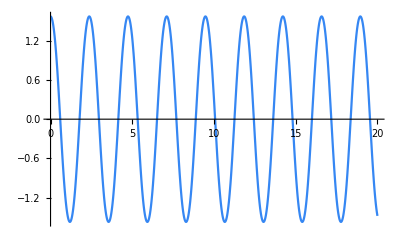

```mathematica
Plot[θ[t]/.sol,{t,0,20}]
```

```mathematica
T[theta0_] := NIntegrate[4*√(L/(2g))1/(√(Cos[θ]-Cos[theta0])),{θ,0,theta0}]
```

```mathematica
T[1.57]
```

2.36862

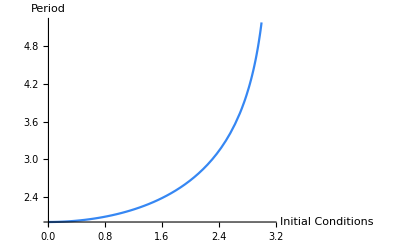

```mathematica
Plot[T[x],{x,0.01,π},AxesLabel->{"Initial Conditions","Period"}]
```